# QEA - Attitude Control - B-set 3

```mathematica
SetDirectory@NotebookDirectory[];
<<"../General.m"
```

## Springy

```mathematica
With[{context="springy`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Solve differential equations with specified initial conditions. Here I want θ'[t]^2 because it should always add to the length of the spring.

```mathematica
With[{m=1,g=9.8,l0=3,k=5},initialConditions={θ[0]==π/2,θ'[0]==0,l[0]==1,l'[0]==0};
de={θ''[t]== (-m g Sin[θ[t]]-2l'[t] θ'[t])/l[t],l''[t]==-k/m(l[t]-l0)+g Cos[θ[t]]+l[t] θ'[t]^2};
{θSol,lSol}=NDSolveValue[Join[initialConditions,de],{θ[t],l[t]},{t,0,30}]
]
```

{InterpolatingFunction[{{0., 30.}}, <>][t],InterpolatingFunction[{{0., 30.}}, <>][t]}

### Plot of the angle over time

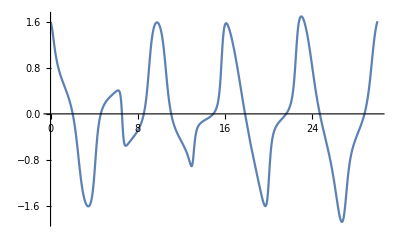

```mathematica
Plot[θSol,{t,0,30},PlotRange->Full]
```

### Plot of the length over time

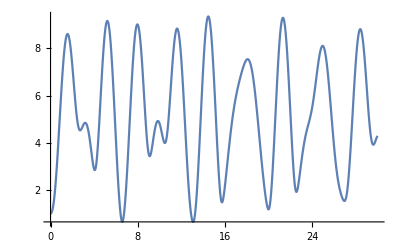

```mathematica
Plot[lSol,{t,0,30},PlotRange->Full]
```

### Animation of springy pendulum

```mathematica
Manipulate[ParametricPlot[{lSol Sin[θSol],-lSol Cos[θSol]},{t,n,n+.1},PlotRange->{{-10,10},{-10,10}}],{n,0,29.9}]
```

### Plot of springy pendulum locations

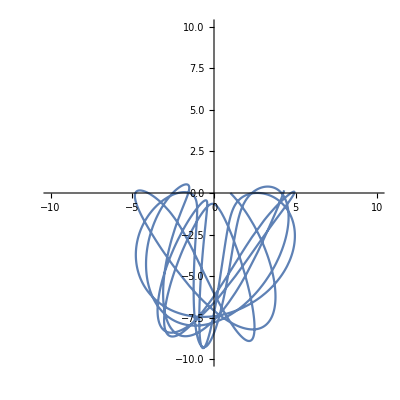

```mathematica
ParametricPlot[{lSol Sin[θSol],-lSol Cos[θSol]},{t,0,30},PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
With[{context="springy`"},If[Context[]==context,End[],"Not in context"]]
```

springy`

## Spinny Springy Pendulum

```mathematica
With[{context="spinnyspringypendulum`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{m=1,g=9.8,l0=1,k=10},initialConditions={θ[0]==π/2,θ'[0]==0,l[0]==1,l'[0]==0,Ω[0]==0,Ω'[0]==(2π)/30};
de={θ''[t]== (-g Sin[θ[t]]-2l'[t] θ'[t]+l[t] Ω'[t]^2 Cos[θ[t]]Sin[θ[t]])/l[t],l''[t]==-k/m(l[t]-l0)+g Cos[θ[t]]+l[t] θ'[t]^2+l[t] Ω'[t]^2 Sin[θ[t]]^2,
Ω''[t]==0};
{θSol,lSol,ΩSol}=NDSolveValue[Join[initialConditions,de],{θ[t],l[t],Ω[t]},{t,0,30}]
]
```

{InterpolatingFunction[{{0., 30.}}, <>][t],InterpolatingFunction[{{0., 30.}}, <>][t],InterpolatingFunction[{{0., 30.}}, <>][t]}

### Plot of the θ over time.

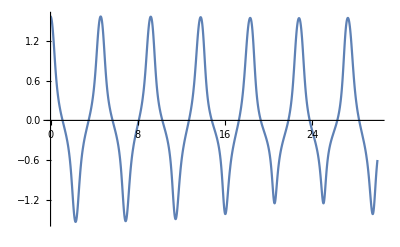

```mathematica
Plot[θSol,{t,0,30},PlotRange->Full]
```

### Plot of the length over time

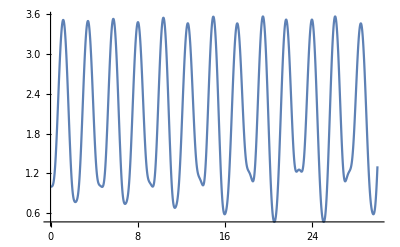

```mathematica
Plot[lSol,{t,0,30},PlotRange->Full]
```

### Plot of Ω over time

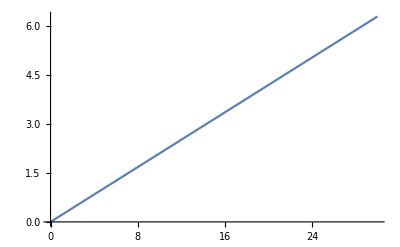

```mathematica
Plot[ΩSol,{t,0,30},PlotRange->Full]
```

### Plot the path of the pendulum

```mathematica
ParametricPlot3D[{lSol Sin[θSol]Cos[ΩSol],lSol Sin[θSol]Sin[ΩSol],-lSol Cos[θSol]},{t,0,30},PlotRange->Full,PlotTheme->"Web"]
```

-Graphics3D-

### Looking down the z axis

### Animation

```mathematica
Manipulate[ParametricPlot3D[{lSol Sin[θSol]Cos[ΩSol],lSol Sin[θSol]Sin[ΩSol],-lSol Cos[θSol]},{t,n,n+.1},PlotRange->{{-1.5,1.5},{-1.5,1.5},{-4,1}}],{n,0,29.9}]
```

```mathematica
With[{context="spinnyspringypendulum`"},If[Context[]==context,End[],"Not in context"]]
```

spinnyspringypendulum`